# Initial conditions

```mathematica
(* For comparison with the analytic solution, keep m1 > m2. Set Rinit and Pinit so that you start at the point of closest distance. Keep PN parameter small: ϵ ->0, P ->0, 1/R -> 0,  spins/(orb. ang. momentum) -> 0*)
```

```mathematica
m1=2.5; m2=1;G=1;ϵ=0.005  ;  spinSuppressFac =  ϵ ;
Q1=2+3 m2/(2 m1);Q2=2+3 m1/(2 m2);
Rinit=1{ 3,0,0};
Pinit=1{0,-1,0};
S1init={0,1,1} spinSuppressFac;
S2init={1,-0.3,0}spinSuppressFac;
Linit=Cross[Rinit,Pinit];
λmax=  100000;
```

# System of equations

```mathematica
R={Rx[λ],Ry[λ],Rz[λ]};P={Px[λ],Py[λ],Pz[λ]};
S1={S1x[λ],S1y[λ],S1z[λ]};S2={S2x[λ],S2y[λ],S2z[λ]};
Seff= Q1 S1 + Q2 S2 ;
L = Cross[R,P] ;


eqa=D[R,λ]-((1/m1 +1/m2)P - (G ϵ (R × Seff))/(R.R)^(3/2));
eqb=D[P,λ] +1/(R.R)^(5/2)G (R(Subscript[m, 1] Subscript[m, 2] R.R+3 ϵ ( - L.Seff))+ϵ  R.R  Cross[P,Seff]) ;
eqc=D[S1,λ]- (ϵ  G Q1 (-(P.S1) R +(R.S1) P))/(R.R)^(3/2);
eqd=D[S2,λ]-(ϵ G Q2 (-(P.S2) R +(R.S2) P))/(R.R)^(3/2);
```

```mathematica
system0={eqa[[1]]==0,eqa[[2]]==0,eqa[[3]]==0, eqb[[1]]==0,eqb[[2]]==0,eqb[[3]]==0,eqc[[1]]==0,eqc[[2]]==0,eqc[[3]]==0,eqd[[1]]==0,eqd[[2]]==0,eqd[[3]]==0}//Simplify;
initCond = {Rx[0] == Rinit[[1]], Ry[0] == Rinit[[2]], Rz[0] == Rinit[[3]], Px[0] == Pinit[[1]], Py[0] == Pinit[[2]], Pz[0] == Pinit[[3]] , S1x[0] ==S1init[[1]], S1y[0] == S1init[[2]], S1z[0] ==S1init[[3]], S2x[0] == S2init[[1]], S2y[0] == S2init[[2]], S2z[0] == S2init[[3]]}  ;
sol=NDSolve[   system0~Join~initCond  ,  {Rx, Ry, Rz, Px, Py,Pz,S1x, S1y, S1z,S2x, S2y, S2z},{λ,0,λmax}];
```

# Parametric plot of trajectory

```mathematica
(*ParametricPlot[Evaluate[{Rx[λ],Ry[λ]}/. sol],{λ,0,λmax}]*)
```

# More plots

```mathematica
(*Plot[{Rx[λ]/.sol,Ry[λ]/.sol,Rz[λ]/.sol},{λ,0,λmax}]
Plot[{Px[λ]/.sol,Py[λ]/.sol,Pz[λ]/.sol},{λ,0,λmax},PlotRange->All]
Plot[Norm[{Rx[λ],Ry[λ],Rz[λ]}]/.sol,{λ,0,λmax}]
Plot[Norm[{Px[λ],Py[λ],Pz[λ]}]/.sol,{λ,0,λmax},PlotRange->All]
Plot[{S1x[λ]/.sol,S1y[λ]/.sol,S1z[λ]/.sol},{λ,0,λmax}]
Plot[{S2x[λ]/.sol,S2y[λ]/.sol,S2z[λ]/.sol},{λ,0,λmax}]*)
```

# Checking the constancy of constants of motion

```mathematica
(*Rvec[t_] := R /.sol[[1]]  /.λ->t
Pvec[t_] := P /.sol[[1]]  /.λ->t
S1vec[t_] := S1 /.sol[[1]]  /.λ->t
S2vec[t_] := S2 /.sol[[1]]  /.λ->t
Lvec[t_]:= Cross[Rvec[t], Pvec[t]]
Jvec[t_] := Lvec[t]+ S1vec[t]+ S2vec[t]
Lnorm[t_]:= Lvec[t]  //Norm
S1norm[t_]:= S1vec[t]  //Norm
S2norm[t_]:= S2vec[t]  //Norm
Seffvec[t_]:= Seff     /.sol[[1]]  /.λ->t
SeffdL[t_] := Seffvec[t].Lvec[t]       
Plot[{Lnorm[t], S1norm[t], S2norm[t], SeffdL[t],  Jvec[t][[1]],Jvec[t][[2]],Jvec[t][[3]]    }, {t,0,λmax}]     *)  (*Everything checks out*)
```

# Evaluation of Cos[κ_1]

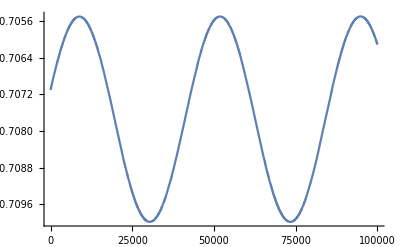

```mathematica
Plot[(Cross[R,P].S1)/(Norm[Cross[R,P]] Norm[S1])/.sol,{λ,0,λmax},PlotRange->All]
```

```mathematica
Quit[];
```